# Percolation on the hexagonal lattice with Dobrushin boundary conditions

## Tim Mesikepp

## First run this code

```mathematica
ExplorerPath[Mat_,SF_]:=Module[{Pts,No=Length[Mat],θs,FirstPt},
θs=ExplorerAngles[Mat];
θs=SF*Table[N[{Cos[θs[[k]] π/3],Sin[θs[[k]] π/3]}],{k,1,Length[θs]}];
PrependTo[θs,(No-1)*{√3,-1}-SF{1,0}];
θs=Accumulate[θs]
];

Bern[p_]:=If[RandomReal[1]<=p,1,0];

ColorTile[n_]:=If[n==0,Blue,Yellow];

ColorsMatrix[n_]:=Module[{BaseM=RandomInteger[1,{n,n}],MultM=ReplacePart[IdentityMatrix[n],{n,n}->0],OneL=Table[1,{k,1,n}]},
BaseM[[1]]=OneL;
BaseM[[All,1]]=OneL;
MultM.BaseM.MultM
];

(* Change probability of yellow tile to p *)
ColorsMatrixP[n_,p_]:=Module[{BaseM=Table[Bern[p],{j,1,n},{k,1,n}],MultM=ReplacePart[IdentityMatrix[n],{n,n}->0],OneL=Table[1,{k,1,n}]},
BaseM[[1]]=OneL;
BaseM[[All,1]]=OneL;
MultM.BaseM.MultM
];

RandomHexagons[n_]:=Module[{ColorsMat},
ColorsMat=ColorsMatrix[n];
Table[{ColorTile[ColorsMat[[i+1,j+1]]],RegularPolygon[i{Sqrt[3],-1}+j{Sqrt[3],1},{1,0},6]},{i,0,n-1},{j,0,n-1}]
];

(* Tracing out the boundary: *)

NextTile[CurrentTile_,Oldθ_,Newθ_]:=Module[{NextTile},
If[Newθ==0,If[Oldθ==1,NextTile=CurrentTile+{1,0},NextTile=CurrentTile+{0,1}],
If[Newθ==1,If[Oldθ==2,NextTile=CurrentTile+{0,1},NextTile=CurrentTile+{-1,1}],
If[Newθ==2,If[Oldθ==3,NextTile=CurrentTile+{-1,1},NextTile=CurrentTile+{-1,0}],
If[Newθ==3,If[Oldθ==4,NextTile=CurrentTile+{-1,0},NextTile=CurrentTile+{0,-1}],
If[Newθ==4,If[Oldθ==5,NextTile=CurrentTile+{0,-1},NextTile=CurrentTile+{1,-1}],
If[Oldθ==0,NextTile=CurrentTile+{1,-1},NextTile=CurrentTile+{1,0}]
]
]
]
]
];
NextTile
];

(* List of arguments (namely, what multiples of π/3) for steps *)

ExplorerAngles[Mat_]:=Module[{θList={1},No=Length[Mat],CT},
CT={No-1,2};
While[CT[[1]]!=0,
If[Mat[[CT[[1]],CT[[2]]]]==0,AppendTo[θList,Mod[Last[θList]+1,6]],AppendTo[θList,Mod[Last[θList]-1,6]]];
CT=NextTile[CT,θList[[-2]],θList[[-1]]]
];
θList
];


(* Simple visualization of hexagons given the color matrix *)

PercPict[Mat_,ImageS_]:=Module[{No=Length[Mat]},
Graphics[{
Table[{ColorTile[Mat[[i+1,j+1]]],RegularPolygon[i{Sqrt[3],-1}+j{Sqrt[3],1},1,6]},{i,0,No-1},{j,0,No-1}]
},
ImageSize->ImageS]
];

(* Visualize interior hexagons given the color matrix.  Here Bound_ is the opacity of the boundary rhombus, and Dobr_ is the opacity of the surrounding Dobrushin boundary hexagons *)

PercPictInt[Mat_,ImageS_,Bound_,Dobr_]:=Module[{No=Length[Mat]},
Graphics[{
Table[{ColorTile[Mat[[i+1,j+1]]],RegularPolygon[i{Sqrt[3],-1}+j{Sqrt[3],1},1,6]},{i,1,No-2},{j,1,No-2}],

(* Dobrushin hexagons*)
{Opacity[Dobr],Table[{ColorTile[Mat[[1,j+1]]],RegularPolygon[0{Sqrt[3],-1}+j{Sqrt[3],1},1,6]},{j,0,No-1}],
Table[{ColorTile[Mat[[i+1,No]]],RegularPolygon[i{Sqrt[3],-1}+(No-1){Sqrt[3],1},1,6]},{i,1,No-1}],
Table[{ColorTile[Mat[[No,j+1]]],RegularPolygon[(No-1){Sqrt[3],-1}+j{Sqrt[3],1},1,6]},{j,0,No-2}],
Table[{ColorTile[Mat[[i+1,1]]],RegularPolygon[i{Sqrt[3],-1}+0{Sqrt[3],1},1,6]},{i,1,No-2}]
},

(* Boundary *)
{Dashed,Opacity[Bound],Line[{1{Sqrt[3],-1}+1{Sqrt[3],1},(No-2){Sqrt[3],-1}+1{Sqrt[3],1},(No-2){Sqrt[3],-1}+(No-2){Sqrt[3],1},1{Sqrt[3],-1}+(No-2){Sqrt[3],1},1{Sqrt[3],-1}+1{Sqrt[3],1}}]}
},
ImageSize->ImageS]
];

(* Visualize hexagons and interface path given color matrix *)

PercPictIntPath[Mat_,ImageS_,Bound_,Dobr_,Thickn_]:=Module[{No=Length[Mat],ExplorerP},
ExplorerP=ExplorerPath[Mat,1.15];

Graphics[{
Table[{ColorTile[Mat[[i+1,j+1]]],RegularPolygon[i{Sqrt[3],-1}+j{Sqrt[3],1},1,6]},{i,1,No-2},{j,1,No-2}],

(* Dobrushin hexagons*)
{Opacity[Dobr],Table[{ColorTile[Mat[[1,j+1]]],RegularPolygon[0{Sqrt[3],-1}+j{Sqrt[3],1},1,6]},{j,0,No-1}],
Table[{ColorTile[Mat[[i+1,No]]],RegularPolygon[i{Sqrt[3],-1}+(No-1){Sqrt[3],1},1,6]},{i,1,No-1}],
Table[{ColorTile[Mat[[No,j+1]]],RegularPolygon[(No-1){Sqrt[3],-1}+j{Sqrt[3],1},1,6]},{j,0,No-2}],
Table[{ColorTile[Mat[[i+1,1]]],RegularPolygon[i{Sqrt[3],-1}+0{Sqrt[3],1},1,6]},{i,1,No-2}]
},

(* Boundary *)
{Dashed,Opacity[Bound],Line[{1{Sqrt[3],-1}+1{Sqrt[3],1},(No-2){Sqrt[3],-1}+1{Sqrt[3],1},(No-2){Sqrt[3],-1}+(No-2){Sqrt[3],1},1{Sqrt[3],-1}+(No-2){Sqrt[3],1},1{Sqrt[3],-1}+1{Sqrt[3],1}}]},

(* Explorer path *)
{Black,Thickness[Thickn],Line[ExplorerP]},
{Red,Thickness[(7/8)Thickn],Line[ExplorerP]}
},
ImageSize->ImageS]
];

(* Visualize hexagons and interface path given color matrix, with option to make hexagons less opaque to see path clearer.  Here all hexagons have opacity equal to Dobr_ *)

PercPictIntPath2[Mat_,ImageS_,Bound_,Dobr_,Thickn_]:=Module[{No=Length[Mat],ExplorerP},
ExplorerP=ExplorerPath[Mat,1.15];

Graphics[{
{Opacity[Dobr],Table[{ColorTile[Mat[[i+1,j+1]]],RegularPolygon[i{Sqrt[3],-1}+j{Sqrt[3],1},1,6]},{i,1,No-2},{j,1,No-2}]},

(* Dobrushin hexagons*)
{Opacity[Dobr],Table[{ColorTile[Mat[[1,j+1]]],RegularPolygon[0{Sqrt[3],-1}+j{Sqrt[3],1},1,6]},{j,0,No-1}],
Table[{ColorTile[Mat[[i+1,No]]],RegularPolygon[i{Sqrt[3],-1}+(No-1){Sqrt[3],1},1,6]},{i,1,No-1}],
Table[{ColorTile[Mat[[No,j+1]]],RegularPolygon[(No-1){Sqrt[3],-1}+j{Sqrt[3],1},1,6]},{j,0,No-2}],
Table[{ColorTile[Mat[[i+1,1]]],RegularPolygon[i{Sqrt[3],-1}+0{Sqrt[3],1},1,6]},{i,1,No-2}]
},

(* Boundary *)
{Dashed,Opacity[Bound],Line[{1{Sqrt[3],-1}+1{Sqrt[3],1},(No-2){Sqrt[3],-1}+1{Sqrt[3],1},(No-2){Sqrt[3],-1}+(No-2){Sqrt[3],1},1{Sqrt[3],-1}+(No-2){Sqrt[3],1},1{Sqrt[3],-1}+1{Sqrt[3],1}}]},

(* Explorer path *)
{Black,Thickness[Thickn],Line[ExplorerP]},
{Red,Thickness[(7/8)Thickn],Line[ExplorerP]}
},
ImageSize->ImageS]
];


(* Visualize hexagons and interface path given color matrix, simpler version *)

PercPictExplorer[Mat_,ImageS_,Thickn_]:=Module[{No=Length[Mat],ExplorerP},
ExplorerP=ExplorerPath[Mat,1.15];
Graphics[{
Table[{ColorTile[Mat[[i+1,j+1]]],RegularPolygon[i{Sqrt[3],-1}+j{Sqrt[3],1},1,6]},{i,0,No-1},{j,0,No-1}],
{Black,Thickness[Thickn],Line[ExplorerP]},
{Red,Thickness[(7/8)Thickn],Line[ExplorerP]}
},
ImageSize->ImageS]
];

(* Include option for making the actual hexagons less opaque to see the line better on large sample sizes *)

PercPictExplorerOp[Mat_,ImageS_,Thickn_,Op_]:=Module[{No=Length[Mat],ExplorerP},
ExplorerP=ExplorerPath[Mat,1.15];
Graphics[{
{Opacity[Op],Table[{ColorTile[Mat[[i+1,j+1]]],RegularPolygon[i{Sqrt[3],-1}+j{Sqrt[3],1},1,6]},{i,0,No-1},{j,0,No-1}]},
{Black,Thickness[Thickn],Line[ExplorerP]},
{Red,Thickness[(7/8)Thickn],Line[ExplorerP]}
},
ImageSize->ImageS]
];

(* Draw Dobrushin boundary *)

PercDobrushinB[n_,ImageS_]:=Graphics[{
{Yellow,Table[RegularPolygon[j{Sqrt[3],1},1,6],{j,0,n-2}],Table[RegularPolygon[i{Sqrt[3],-1},1,6],{i,0,n-2}]},
{Blue,Table[RegularPolygon[(n-1){Sqrt[3],-1}+j{Sqrt[3],1},1,6],{j,0,n-1}],Table[RegularPolygon[i{Sqrt[3],-1}+(n-1){Sqrt[3],1},1,6],{i,0,n-1}]}
},
ImageSize->ImageS
]
```

Null^2

## Then see it in action

First, create the “colors matrix” - which says whether or not each hexagon is open or closed.  This fixes the same and then the same colors matrix can be visualized in different ways.  The input variable is the dimension - in this case 50 x 50

```mathematica
Mat1=ColorsMatrix[100];
```

Now, one option of visualization: The input variables are the name of the colors matrix, then the desired image output size, and then the width of the discrete SLE path the traces the interface boundary.

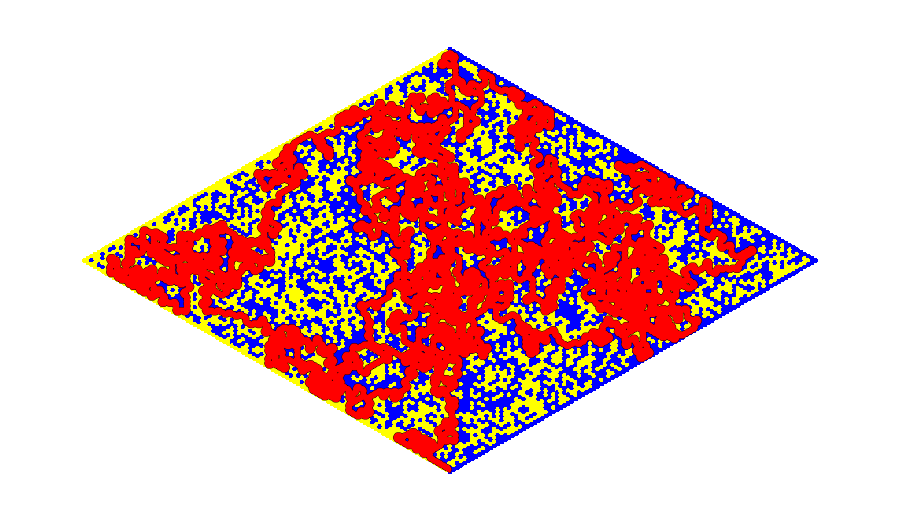

```mathematica
PercPictExplorer[Mat1,900,0.005]
```

There are some other options for visualization that you can decipher by directly reading the code in the first section.